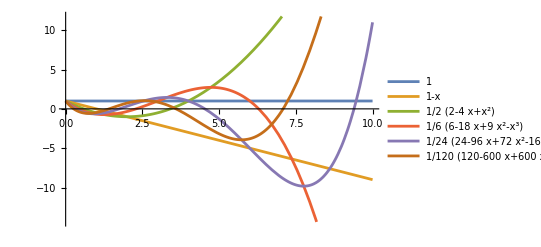

```mathematica
Plot[Evaluate[Table[LaguerreL[n,x],{n,0,5}]],{x,0,10},PlotLegends->"Expressions"]
```

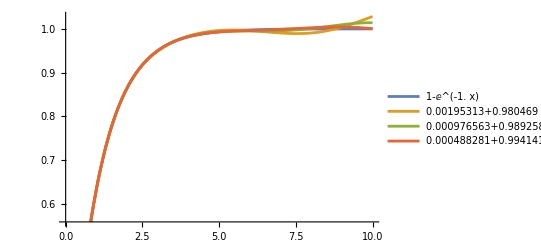

```mathematica
gamma=1.0;
y[x_] := 1 - Exp[-x/gamma];
c=Table[NIntegrate[LaguerreL[n,x]*y[x]*Exp[-x],{x,0,Infinity}],{n,0,11}];
yy[x_,m_]:=Sum[c[[n+1]] LaguerreL[n,x],{n,0,m}];
Plot[Evaluate[Simplify[Prepend[Table[yy[x,m],{m,8,10}],y[x]]]],{x,0,10},PlotLegends->"Expressions"]
```